FCC Symmetry Points:

Γ  = 2π { 0.0 , 0.0 , 0.0 } 
W = 2π { 0.5 , 0.0 , 1.0 }
X =  2π  { 0.0 , 0.0 , 1.0 }
L =  2π  { 0.5 , 0.5 , 0.5 }
Κ =  2π  { 0.25 , 0.25 , 1 }

## (Γ - X) Silicon

```mathematica
ClearAll["Global`*"]
a=5.43;
b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};
maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};

dk=0.01;
path=(2π)/a*Table[{i,0,0},{i,0.,3.,dk}];
pathdistance=path;

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=ConstantArray[0.,Length[path]];
Do[
H=ConstantArray[0.,{lG,lG}];

Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

H⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3., 2*Cos[q.t]* (-1.43),
qn==(2.*π)/a*√8., 2*Cos[q.t]* (0.27),
qn==(2.*π)/a*√11., 2*Cos[q.t]* (0.54),
True,0.]
,{i,lG},{j,lG}];

energy⟦m⟧=Sort[Eigenvalues[H]]⟦Range[n,n+4]⟧;
,{m,Length[path]}]

topvalence=energy⟦1,2⟧;
plot=ConstantArray[0.,5];
Do[plot⟦i⟧=ListLinePlot[Table[{pathdistance⟦k⟧,energy⟦k,i⟧-topvalence},{k,Length[path]}],
PlotStyle->Black,PlotRange->All],
{i,Length[plot]}]
```

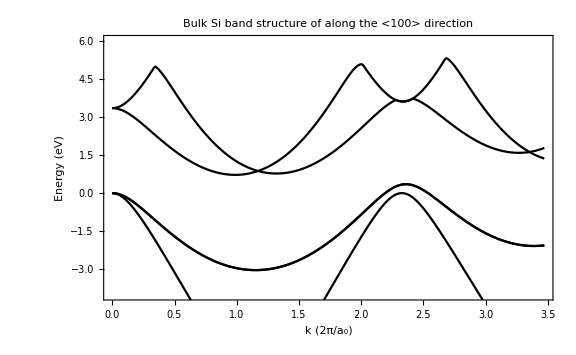

```mathematica
Show[plot,PlotRange-> {All,{-4,6}},Frame-> True,FrameLabel-> {"k (2π/a_0)", "Energy (eV)"},PlotLabel-> "Bulk Si band structure of along the <100> direction"]
```

## (L-Γ-X) Silicon

```mathematica
ClearAll["Global`*"]
a=5.43;
b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};
maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};
(*------------------Generate Path----------------------*)

symmetrypoints = (2π)/a*{{0.5,0.5,0.5},{0.0,0.0,0.0},{0.0,0.0,1.0}};
kdirections=ConstantArray[0.0,Length[symmetrypoints]-1];

np=100;
path=pathdistance=ConstantArray[0.0,{(Length[symmetrypoints]-1)*np}];

Do[
(* Direction vectors to generate the path in k-space *)
kdirections⟦i⟧=1/np*(symmetrypoints⟦i+1⟧-symmetrypoints⟦i⟧)
,{i,Length[symmetrypoints]-1}]; 

Do[
(* path in k-space, each iteration assigns n elements of the path from one symmetry point to the next symmetry point *)
path⟦Range[(m-1)*np+1,m*np]⟧=ConstantArray[symmetrypoints⟦m⟧,np]+Table[kdirections⟦m⟧*l,{l,0.,np-1}]; 
,{m,Length[symmetrypoints]-1}]

pathdistance⟦1⟧=-0.9;
Do[
(* total distance moved from the start till reaching each point k *)
pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧], 
{i,2,Length[pathdistance]}];

(*------------------End Path----------------------*)

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=ConstantArray[0.,Length[path]];
Do[
H=ConstantArray[0.,{lG,lG}];

Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

H⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3., 2*Cos[q.t]* (-1.43),
qn==(2.*π)/a*√8., 2*Cos[q.t]* (0.27),
qn==(2.*π)/a*√11., 2*Cos[q.t]* (0.54),
True,0.]
,{i,lG},{j,lG}];

energy⟦m⟧=Sort[Eigenvalues[H]]⟦Range[n,n+4]⟧;
,{m,Length[path]}]

topvalence=Max[energy⟦All,2⟧];
plot=ConstantArray[0.,5];
Do[plot⟦i⟧=ListLinePlot[Table[{pathdistance⟦k⟧,energy⟦k,i⟧-topvalence},{k,Length[path]}],
PlotStyle->Black],
{i,Length[plot]}]
```

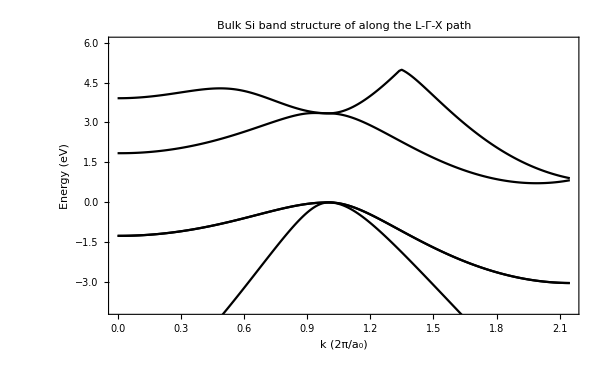

```mathematica
Show[plot,PlotRange-> {All,{-4,6}},Frame-> True,FrameLabel-> {"k (2π/a_0)", "Energy (eV)"},PlotLabel-> "Bulk Si band structure of along the L-Γ-X path"]
```

## (L-Γ-X) Germanium

```mathematica
ClearAll["Global`*"]
a=5.43;
b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};
maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};
(*------------------Generate Path----------------------*)
symmetrypoints = (2π)/a*{{0.5,0.5,0.5},{0.0,0.0,0.0},{0.0,0.0,1.0}};
kdirections=ConstantArray[0.0,Length[symmetrypoints]-1];

np=100;
path=pathdistance=ConstantArray[0.0,{(Length[symmetrypoints]-1)*np}];

Do[
(* Direction vectors to generate the path in k-space *)
kdirections⟦i⟧=1/np*(symmetrypoints⟦i+1⟧-symmetrypoints⟦i⟧)
,{i,Length[symmetrypoints]-1}]; 

Do[
(* path in k-space, each iteration assigns n elements of the path from one symmetry point to the next symmetry point *)
path⟦Range[(m-1)*np+1,m*np]⟧=ConstantArray[symmetrypoints⟦m⟧,np]+Table[kdirections⟦m⟧*l,{l,0.,np-1}]; 
,{m,Length[symmetrypoints]-1}]

pathdistance⟦1⟧=-0.9;
Do[
(* total distance moved from the start till reaching each point k *)
pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧], 
{i,2,Length[pathdistance]}];

(*------------------End Path----------------------*)

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=ConstantArray[0.,Length[path]];
Do[
H=ConstantArray[0.,{lG,lG}];

Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

H⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3., 2*Cos[q.t]* (-1.57),
qn==(2.*π)/a*√8., 2*Cos[q.t]* (0.07),
qn==(2.*π)/a*√11., 2*Cos[q.t]* (0.41),
True,0.]
,{i,lG},{j,lG}];

energy⟦m⟧=Sort[Eigenvalues[H]]⟦Range[n,n+4]⟧;
,{m,Length[path]}]

topvalence=Max[energy⟦All,2⟧];
plot=ConstantArray[0.,5];
Do[plot⟦i⟧=ListLinePlot[Table[{pathdistance⟦k⟧,energy⟦k,i⟧-topvalence},{k,Length[path]}],
PlotStyle->Black],
{i,Length[plot]}]
```

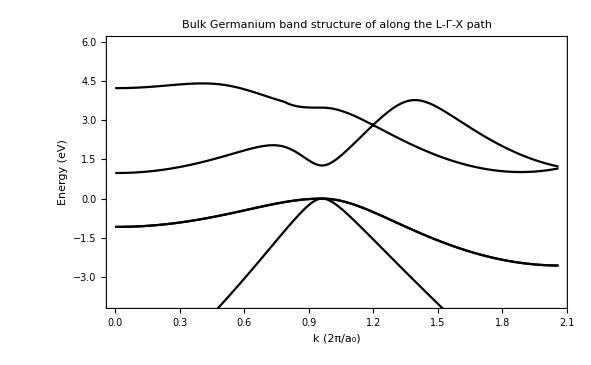

```mathematica
Show[plot,PlotRange-> {All,{-4,6}},Frame-> True,
FrameLabel-> {"k (2π/a_0)", "Energy (eV)"},PlotLabel-> "Bulk Germanium band structure of along the L-Γ-X path"]
```

## Charge Densities (Silicon)

```mathematica
ClearAll["Global`*"]
a=5.43;
b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};
maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};

dk=1.;
path=(2π)/a*Table[{i,0,0},{i,0.,.1,dk}];
pathdistance=path;

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=vectors=ConstantArray[0.,Length[path]];
Do[
H=ConstantArray[0.,{lG,lG}];

Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

H⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3., 2*Cos[q.t]* (-1.43),
qn==(2.*π)/a*√8., 2*Cos[q.t]* (0.27),
qn==(2.*π)/a*√11., 2*Cos[q.t]* (0.54),
True,0.]
,{i,lG},{j,lG}];

energy⟦m⟧=Eigenvalues[H]⟦-Range[4]⟧;
vectors⟦m⟧=Eigenvectors[H]⟦-Range[4]⟧
,{m,Length[path]}]
```

## Calculating Charge Density

```mathematica
ψ10[x_,y_,z_]:=vectors⟦1,1⟧.ⅇ^(ⅈ*G.{x,y,z});
ψ20[x_,y_,z_]:=vectors⟦1,2⟧.ⅇ^(ⅈ*G.{x,y,z});
ψ30[x_,y_,z_]:=vectors⟦1,3⟧.ⅇ^(ⅈ*G.{x,y,z});
ψ40[x_,y_,z_]:=vectors⟦1,4⟧.ⅇ^(ⅈ*G.{x,y,z});
ρ[x_,y_,z_]:=ψ10[x,y,z]*ψ10[x,y,z]*+ψ20[x,y,z]*ψ20[x,y,z]*+ψ30[x,y,z]*ψ30[x,y,z]*+ψ40[x,y,z]*ψ40[x,y,z]*;

z=a*{0.,0.125,0.25,0.375,0.5};
plot=0.*z;

Do[
plot⟦i⟧=ContourPlot[ρ[x,y,z⟦i⟧],{x,0.,a},{y,0.,a}]
,{i,Length[z]}]
```

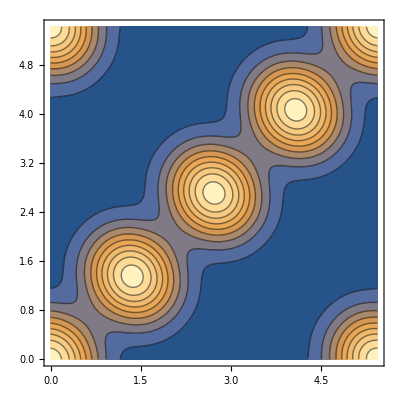
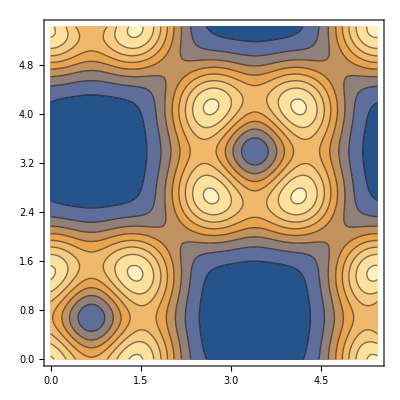
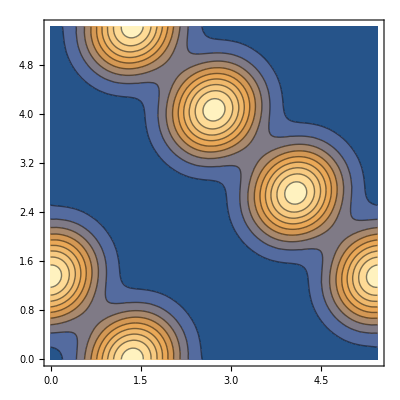
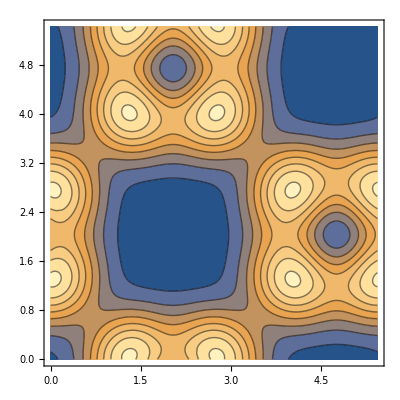
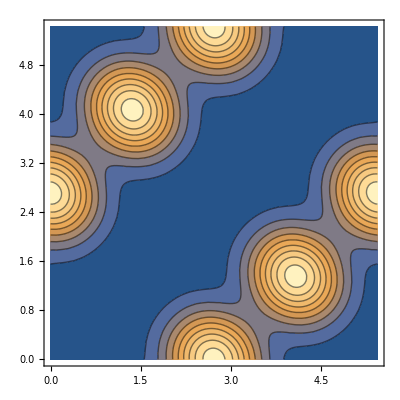

```mathematica
plot
```

## (L - Γ - X) GaAs

```mathematica
ClearAll["Global`*"]
a=5.43;
b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};
maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};
(*------------------Generate Path----------------------*)

symmetrypoints = (2π)/a*{{0.5,0.5,0.5},{0.0,0.0,0.0},{0.0,0.0,1.0}};
kdirections=ConstantArray[0.0,Length[symmetrypoints]-1];

np=200;
path=pathdistance=ConstantArray[0.0,{(Length[symmetrypoints]-1)*np}];

Do[
(* Direction vectors to generate the path in k-space *)
kdirections⟦i⟧=1/np*(symmetrypoints⟦i+1⟧-symmetrypoints⟦i⟧)
,{i,Length[symmetrypoints]-1}]; 

Do[
(* path in k-space, each iteration assigns n elements of the path from one symmetry point to the next symmetry point *)
path⟦Range[(m-1)*np+1,m*np]⟧=ConstantArray[symmetrypoints⟦m⟧,np]+Table[kdirections⟦m⟧*l,{l,0.,np-1}]; 
,{m,Length[symmetrypoints]-1}]

pathdistance⟦1⟧=-0.9;
Do[
(* total distance moved from the start till reaching each point k *)
pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧], 
{i,2,Length[pathdistance]}];

(*------------------End Path----------------------*)

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=ConstantArray[0.,Length[path]];
Do[
H=ConstantArray[0.,{lG,lG}];

Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

H⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3., Cos[q.t]* (-3.13)+ⅈ Sin[q.t]*(0.95),
qn==(2.*π)/a*√8., Cos[q.t]* (0.14),
qn==(2.*π)/a*2.,ⅈ*Sin[q.t]* (0.68),
qn==(2.*π)/a*√11., Cos[q.t]*(0.82)+ⅈ Sin[q.t]*(0.14),
True,0.]
,{i,lG},{j,lG}];

energy⟦m⟧=Sort[Eigenvalues[H]]⟦Range[n,n+4]⟧;
,{m,Length[path]}]

topvalence=Max[energy⟦All,2⟧];
plot=ConstantArray[0.,5];
Do[plot⟦i⟧=ListLinePlot[Table[{pathdistance⟦k⟧,energy⟦k,i⟧-topvalence},{k,Length[path]}],
PlotStyle->Black],
{i,Length[plot]}]
```

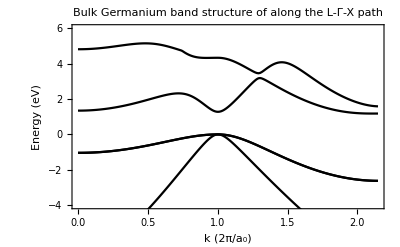

```mathematica
Show[plot,PlotRange-> {All,{-4,6}},Frame-> True,
FrameLabel-> {"k (2π/a_0)", "Energy (eV)"},PlotLabel-> "Bulk Germanium band structure of along the L-Γ-X path"]
```

## Calculating Effective Mass GaAs

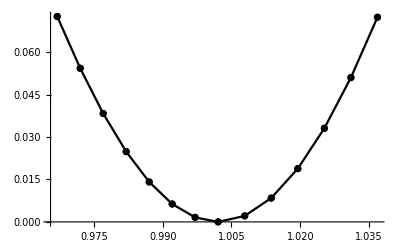

0.0639636

```mathematica
mid = Floor[Length[pathdistance]/2.];kem=pathdistance⟦Range[mid-6,mid+7]⟧;
enem=energy⟦Range[mid-6,mid+7],4⟧-Min[energy⟦Range[mid-6,mid+7],4⟧];
data=Table[{kem⟦i⟧,enem⟦i⟧},{i,Length[kem]}];
ListPlot[data,PlotStyle-> Black,Joined->True,Mesh->Full]

emodel = 0.5*Coefficient[D[Fit[data,{1,x,x^2},x],x],x];
meff = hom/(2*emodel)
```

## (L - Γ - X) InAs

```mathematica
ClearAll["Global`*"]
a=6.0583;
b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};
maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};
(*------------------Generate Path----------------------*)

symmetrypoints = (2π)/a*{{0.5,0.5,0.5},{0.0,0.0,0.0},{0.0,0.0,1.0}};
kdirections=ConstantArray[0.0,Length[symmetrypoints]-1];

np=100;
path=pathdistance=ConstantArray[0.0,{(Length[symmetrypoints]-1)*np}];

Do[
(* Direction vectors to generate the path in k-space *)
kdirections⟦i⟧=1/np*(symmetrypoints⟦i+1⟧-symmetrypoints⟦i⟧)
,{i,Length[symmetrypoints]-1}]; 

Do[
(* path in k-space, each iteration assigns n elements of the path from one symmetry point to the next symmetry point *)
path⟦Range[(m-1)*np+1,m*np]⟧=ConstantArray[symmetrypoints⟦m⟧,np]+Table[kdirections⟦m⟧*l,{l,0.,np-1}]; 
,{m,Length[symmetrypoints]-1}]

pathdistance⟦1⟧=-0.9;
Do[
(* total distance moved from the start till reaching each point k *)
pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧], 
{i,2,Length[pathdistance]}];

(*------------------End Path----------------------*)

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=ConstantArray[0.,Length[path]];
Do[
H=ConstantArray[0.,{lG,lG}];

Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

H⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3., Cos[q.t]* (-2.99)+ⅈ Sin[q.t]*(1.09),
qn==(2.*π)/a*√8., Cos[q.t]* (0.0),
qn==(2.*π)/a*2.,ⅈ*Sin[q.t]* (0.68),
qn==(2.*π)/a*√11., Cos[q.t]*(0.68)+ⅈ Sin[q.t]*(0.41),
True,0.]
,{i,lG},{j,lG}];

energy⟦m⟧=Sort[Eigenvalues[H]]⟦Range[n,n+4]⟧;
,{m,Length[path]}]

topvalence=Max[energy⟦All,2⟧];
plot=ConstantArray[0.,5];
Do[plot⟦i⟧=ListLinePlot[Table[{pathdistance⟦k⟧,energy⟦k,i⟧-topvalence},{k,Length[path]}],
PlotStyle->Black],
{i,Length[plot]}]
```

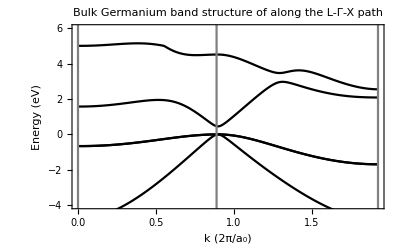

```mathematica
Show[plot,
ListLinePlot[{{0,-10},{0,10}},PlotStyle->Gray],
ListLinePlot[{{pathdistance⟦100⟧,-10},{pathdistance⟦100⟧,10}},PlotStyle->Gray],
ListLinePlot[{{pathdistance⟦200⟧,-10},{pathdistance⟦200⟧,10}},PlotStyle->Gray],PlotRange-> {All,{-4,6}},Frame-> True,
FrameLabel-> {"k (2π/a_0)", "Energy (eV)"},PlotLabel-> "Bulk Germanium band structure of along the L-Γ-X path"]
```

## Charge Densities GaAs

```mathematica
ClearAll["Global`*"]
a=5.43;
b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};
maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};

dk=1.;
path=(2π)/a*Table[{i,0,0},{i,0.,.1,dk}];
pathdistance=path;

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=vectors=ConstantArray[0.,Length[path]];
Do[
H=ConstantArray[0.,{lG,lG}];

Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

H⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3., Cos[q.t]* (-3.13)+ⅈ Sin[q.t]*(0.95),
qn==(2.*π)/a*√8., Cos[q.t]* (0.14),
qn==(2.*π)/a*2.,ⅈ*Sin[q.t]* (0.68),
qn==(2.*π)/a*√11., Cos[q.t]*(0.82)+ⅈ Sin[q.t]*(0.14),
True,0.]
,{i,lG},{j,lG}];

energy⟦m⟧=Eigenvalues[H]⟦-Range[4]⟧;
vectors⟦m⟧=Eigenvectors[H]⟦-Range[4]⟧
,{m,Length[path]}]
```

```mathematica
ψ10[x_,y_,z_]:=vectors⟦1,1⟧.ⅇ^(ⅈ*G.{x,y,z});
ψ20[x_,y_,z_]:=vectors⟦1,2⟧.ⅇ^(ⅈ*G.{x,y,z});
ψ30[x_,y_,z_]:=vectors⟦1,3⟧.ⅇ^(ⅈ*G.{x,y,z});
ψ40[x_,y_,z_]:=vectors⟦1,4⟧.ⅇ^(ⅈ*G.{x,y,z});
ρ[x_,y_,z_]:=ψ10[x,y,z]*ψ10[x,y,z]*+ψ20[x,y,z]*ψ20[x,y,z]*+ψ30[x,y,z]*ψ30[x,y,z]*+ψ40[x,y,z]*ψ40[x,y,z]*;

z=a*{0.,0.125,0.25,0.375,0.5};
plot=0.*z;

Do[
plot⟦i⟧=ContourPlot[ρ[x,y,z⟦i⟧],{x,0.,a},{y,0.,a}]
,{i,Length[z]}]
```

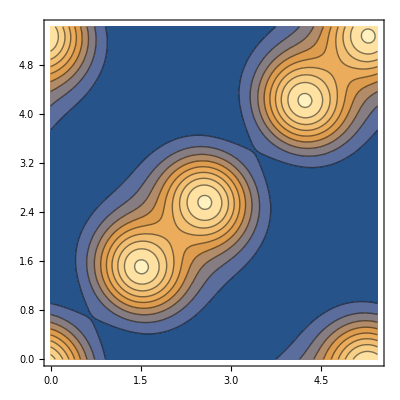
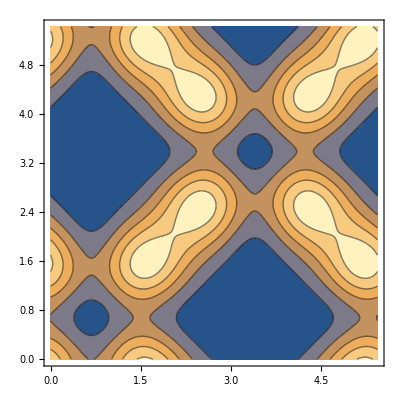
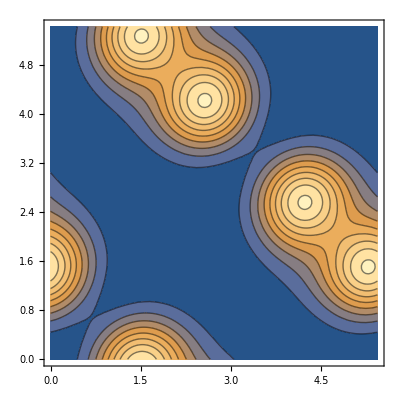
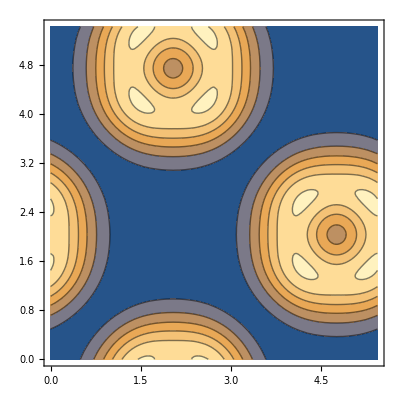
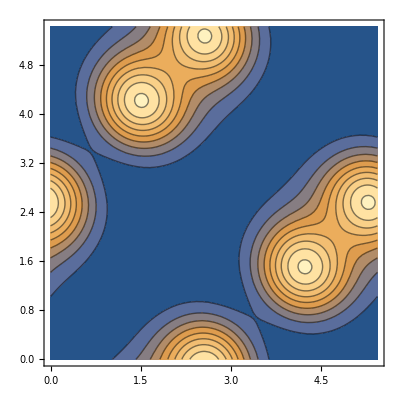

```mathematica
plot
```

```mathematica
0.0002*13.605
```

0.002721

## Spin–orbit coupling in CdTe

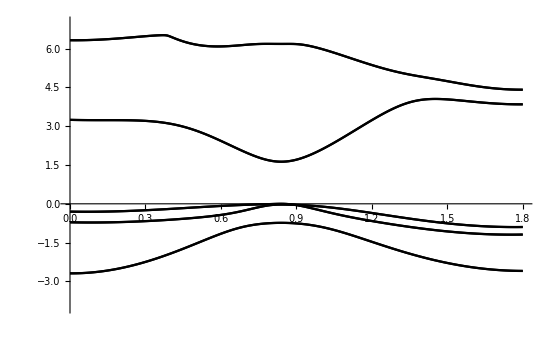

```mathematica
ClearAll["Global`*"]
a=6.48;
λs=0.343*0.02721;
λas=0.343*0.002721;
λc=λs-λas;
λa=λs+λas;

vsym=13.605*{-0.20,-0.151,0.00,0.04};
vanti=13.605*{0.15,0.09,0.0585,0.04};

b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};

maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};
(*------------------Generate Path----------------------*)

symmetrypoints = (2π)/a*{{0.5,0.5,0.5},{0.0,0.0,0.0},{0.0,0.0,1.0}};
kdirections=ConstantArray[0.0,Length[symmetrypoints]-1];

np=100;
path=pathdistance=ConstantArray[0.0,{(Length[symmetrypoints]-1)*np}];

Do[
(* Direction vectors to generate the path in k-space *)
kdirections⟦i⟧=1/np*(symmetrypoints⟦i+1⟧-symmetrypoints⟦i⟧)
,{i,Length[symmetrypoints]-1}]; 

Do[
(* path in k-space, each iteration assigns n elements of the path from one symmetry point to the next symmetry point *)
path⟦Range[(m-1)*np+1,m*np]⟧=ConstantArray[symmetrypoints⟦m⟧,np]+Table[kdirections⟦m⟧*l,{l,0.,np-1}]; 
,{m,Length[symmetrypoints]-1}]

pathdistance⟦1⟧=-0.9;
Do[
(* total distance moved from the start till reaching each point k *)
pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧], 
{i,2,Length[pathdistance]}];

(*------------------End Path----------------------*)

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=ConstantArray[0.,Length[path]];
Do[
Hd=HSOdiag=Hso=ConstantArray[0.,{lG,lG}];
Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

Hd⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3.,0.5 * ⅇ^(ⅈ q.t)*(vsym⟦1⟧-vanti⟦1⟧)+ 0.5* ⅇ^(-ⅈ q.t)*(vsym⟦1⟧+vanti⟦1⟧),
qn==(2.*π)/a*2. ,0.5 * ⅇ^(ⅈ q.t)*(vsym⟦2⟧-vanti⟦2⟧)+ 0.5* ⅇ^(-ⅈ q.t)*(vsym⟦2⟧+vanti⟦2⟧),
qn==(2.*π)/a*√8.,0.5 * ⅇ^(ⅈ q.t)*(vsym⟦3⟧-vanti⟦3⟧)+ 0.5* ⅇ^(-ⅈ q.t)*(vsym⟦3⟧+vanti⟦3⟧),
qn==(2.*π)/a*√11.,0.5 * ⅇ^(ⅈ q.t)*(vsym⟦4⟧-vanti⟦4⟧)+ 0.5* ⅇ^(-ⅈ q.t)*(vsym⟦4⟧+vanti⟦4⟧),
True,0.];
,{i,lG},{j,lG}];

Do[Do[ 
q=-G⟦j⟧+G⟦i⟧;
cross = (G⟦j⟧+path⟦m⟧)×(G⟦i⟧+path⟦m⟧)/(2.π/a)^2;
HSOdiag⟦j,i⟧=-0.5ⅈ*cross⟦3⟧(ⅇ^(ⅈ q.t)*λc+ⅇ^(-ⅈ q.t)*λa );
HSOdiag⟦i,j⟧=HSOdiag⟦j,i⟧*;
Hso⟦j,i⟧ = -0.5ⅈ*(cross⟦1⟧-ⅈ cross⟦2⟧)(ⅇ^(ⅈ q.t)*λc+ⅇ^(-ⅈ q.t)*λa);
Hso⟦i,j⟧=-Hso⟦j,i⟧;
,{i,j}],{j,lG}];

H=ConstantArray[0.0,{2*lG,2*lG}];
H⟦Range[lG],Range[lG]⟧=Hd+HSOdiag;
H⟦Range[lG],Range[lG+1,2*lG]⟧=Hso;
H⟦Range[lG+1,2*lG],Range[lG]⟧=Transpose[Hso]*;
H⟦Range[lG+1,2*lG],Range[lG+1,2*lG]⟧=Hd-HSOdiag;

energy⟦m⟧=Sort[Eigenvalues[H]]⟦Range[12]⟧;
,{m,Length[path]}]

topvalence = Max[energy⟦All,8⟧];
plot=ConstantArray[0.,12];
Do[plot⟦i⟧=ListLinePlot[Table[{pathdistance⟦k⟧,energy⟦k,i⟧-topvalence},{k,Length[path]}],
PlotStyle->Black,PlotRange->{-4,7}],
{i,1,Length[plot]}]

Show[plot,
ListLinePlot[{{0,-10},{0,10}},PlotStyle->Gray],
ListLinePlot[{{pathdistance⟦100⟧,-10},{pathdistance⟦100⟧,10}},PlotStyle->Gray],
ListLinePlot[{{pathdistance⟦200⟧,-10},{pathdistance⟦200⟧,10}},PlotStyle->Gray],PlotRange-> {-4,7}]
```

```mathematica
ClearAll["Global`*"]
a=6.48;
λs=0.343*0.0;
λas=0.343*0.0;
λc=λs-λas;
λa=λs+λas;

vsym=13.605*{-0.20,-0.151,0.00,0.04};
vanti=13.605*{0.15,0.09,0.0585,0.04};

b1={1,1,-1};
b2={1,-1,1};
b3={-1,1,1};

maxi=4;
G=ConstantArray[0.,(2*maxi+1)^3];
m=1;
Do[
G⟦m⟧=i*b1+j*b2+k*b3;
m++;
,{i,-4,4},{j,-4,4},{k,-4,4}]
G=(2*π)/a*SortBy[G,Norm,NumericalOrder]⟦Range[65]⟧;

n=2;
hom=7.62559;
lG=Length[G];
t=a/8.*{1,1,1};
(*------------------Generate Path----------------------*)

symmetrypoints = (2π)/a*{{0.5,0.5,0.5},{0.0,0.0,0.0},{0.0,0.0,1.0}};
kdirections=ConstantArray[0.0,Length[symmetrypoints]-1];

np=100;
path=pathdistance=ConstantArray[0.0,{(Length[symmetrypoints]-1)*np}];

Do[
(* Direction vectors to generate the path in k-space *)
kdirections⟦i⟧=1/np*(symmetrypoints⟦i+1⟧-symmetrypoints⟦i⟧)
,{i,Length[symmetrypoints]-1}]; 

Do[
(* path in k-space, each iteration assigns n elements of the path from one symmetry point to the next symmetry point *)
path⟦Range[(m-1)*np+1,m*np]⟧=ConstantArray[symmetrypoints⟦m⟧,np]+Table[kdirections⟦m⟧*l,{l,0.,np-1}]; 
,{m,Length[symmetrypoints]-1}]

pathdistance⟦1⟧=-0.9;
Do[
(* total distance moved from the start till reaching each point k *)
pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧], 
{i,2,Length[pathdistance]}];

(*------------------End Path----------------------*)

pathdistance⟦1⟧=0.;
Do[pathdistance⟦i⟧=pathdistance⟦i-1⟧+Norm[path⟦i⟧-path⟦i-1⟧],{i,2,Length[pathdistance]}]

energy=ConstantArray[0.,Length[path]];
Do[
Hd=HSOdiag=Hso=ConstantArray[0.,{lG,lG}];
Do[
q=G⟦j⟧-G⟦i⟧;
qn=Norm[q];

Hd⟦i,j⟧=Which[
qn==0. ,0.5*hom*(G⟦i⟧+path⟦m⟧).(G⟦i⟧+path⟦m⟧),
qn==(2.*π)/a*√3.,0.5 * ⅇ^(ⅈ q.t)*(vsym⟦1⟧-vanti⟦1⟧)+ 0.5* ⅇ^(-ⅈ q.t)*(vsym⟦1⟧+vanti⟦1⟧),
qn==(2.*π)/a*2. ,0.5 * ⅇ^(ⅈ q.t)*(vsym⟦2⟧-vanti⟦2⟧)+ 0.5* ⅇ^(-ⅈ q.t)*(vsym⟦2⟧+vanti⟦2⟧),
qn==(2.*π)/a*√8.,0.5 * ⅇ^(ⅈ q.t)*(vsym⟦3⟧-vanti⟦3⟧)+ 0.5* ⅇ^(-ⅈ q.t)*(vsym⟦3⟧+vanti⟦3⟧),
qn==(2.*π)/a*√11.,0.5 * ⅇ^(ⅈ q.t)*(vsym⟦4⟧-vanti⟦4⟧)+ 0.5* ⅇ^(-ⅈ q.t)*(vsym⟦4⟧+vanti⟦4⟧),
True,0.];
,{i,lG},{j,lG}];

Do[Do[ 
q=-G⟦j⟧+G⟦i⟧;
cross = (G⟦j⟧+path⟦m⟧)×(G⟦i⟧+path⟦m⟧)/(2.π/a)^2;
HSOdiag⟦j,i⟧=-0.5ⅈ*cross⟦3⟧(ⅇ^(ⅈ q.t)*λc+ⅇ^(-ⅈ q.t)*λa );
HSOdiag⟦i,j⟧=HSOdiag⟦j,i⟧*;
Hso⟦j,i⟧ = -0.5ⅈ*(cross⟦1⟧-ⅈ cross⟦2⟧)(ⅇ^(ⅈ q.t)*λc+ⅇ^(-ⅈ q.t)*λa);
Hso⟦i,j⟧=-Hso⟦j,i⟧;
,{i,j}],{j,lG}];

H=ConstantArray[0.0,{2*lG,2*lG}];
H⟦Range[lG],Range[lG]⟧=Hd+HSOdiag;
H⟦Range[lG],Range[lG+1,2*lG]⟧=Hso;
H⟦Range[lG+1,2*lG],Range[lG]⟧=Transpose[Hso]*;
H⟦Range[lG+1,2*lG],Range[lG+1,2*lG]⟧=Hd-HSOdiag;

energy⟦m⟧=Sort[Eigenvalues[H]]⟦Range[12]⟧;
,{m,Length[path]}]

topvalence = Max[energy⟦All,8⟧];
plot=ConstantArray[0.,12];
Do[plot⟦i⟧=ListLinePlot[Table[{pathdistance⟦k⟧,energy⟦k,i⟧-topvalence},{k,Length[path]}],
PlotStyle->Black,PlotRange->{-4,7}],
{i,1,Length[plot]}]

Show[plot,
ListLinePlot[{{0,-10},{0,10}},PlotStyle->Gray],
ListLinePlot[{{pathdistance⟦100⟧,-10},{pathdistance⟦100⟧,10}},PlotStyle->Gray],
ListLinePlot[{{pathdistance⟦200⟧,-10},{pathdistance⟦200⟧,10}},PlotStyle->Gray],
PlotRange-> {-4,7}]
```